## I. Observational NAV

## I.1. Kernel Density Estimation for the distribution

```mathematica
Clear[distributionSilverman, plotBlueZero, statusKDE];

distributionSilverman[dataForKDE_] := distributionSilverman[dataForKDE] = SmoothKernelDistribution[
  dataForKDE, 
  silvermanBw[dataForKDE], 
  "Gaussian", 
  MaxExtraBandwidths -> {{0,0}, {2,2}}, 
  (* No extension for the horizontal axis: there cannot be data lower than 0 and higher than 1,
   extension of 2 bandwidths in the vertical axis: relevant for a few models.*)
  InterpolationPoints -> 200
]; (*Apart from MaxExtraBandwidths and InterpolationPoints, these are the standard options for SmoothKernelDistribution*)
  

plotBlueZero[dataForKDE_, opts:OptionsPattern[]] := nListPlot[
  {dataForKDE}, 
  PlotMarkers -> {
    Graphics[{Darker[Blue],Opacity[0.05],Disk[]}, ImageSize -> 10], 
    Graphics[{Darker[Red],Opacity[0.3],Disk[]}, ImageSize -> 10]
  },
  opts,
  PlotRange -> {{0,1}, All},
  AspectRatio -> 1
];

statusKDE[dataForKDE_, {{xmin_, xmax_}, {ymin_, ymax_}}]:= Block[{},
  Echo[silvermanBw[dataForKDE], 
    "Gaussian bandwidths from Silverman rule of thumb: "
  ];
  Print@GraphicsRow[
    {
      plotBlueZero[dataForKDE], 
      ContourPlot[PDF[distributionSilverman[dataForKDE], {x, y}], {x, xmin, xmax}, {y, ymin, ymax}]
    }
  ]
];


(* SPECIFIC DEFINITIONS *)

Clear[gdRList, gdRListFlat];

gdRList[gdFunction_] := gdRList[gdFunction] = gdFunction[{nRad, δVms}][[#]] & /@ Range[175];
gdRListFlat[gdFunction_] := Flatten[gdRList[gdFunction], 1];

list2RARRot = gdRListFlat @ gdR;
list2RARRotNoBulge = gdRListFlat @ gdRBulgeless; 


(*EXECUTION*)

distRARRot = distributionSilverman[list2RARRot];
distRARRotNoBulge = distributionSilverman[list2RARRotNoBulge];

(*Echo["All RAR galaxies case:"];
statusKDE[list2RARRot, {{0, 1}, {-0.5, 1.5}}];
Echo["Only the bulgeless RAR galaxies:"];
statusKDE[list2RARRotNoBulge, {{-0.01,1}, {-0.5, 1.5}}];*)
```

## I.2. The 1σ and 2σ Highest Density Regions

```mathematica
Clear[plotBlue, plotSigmaContours, plotBlueFunction];
(*list1LimitingPDFValues::usage = 
  "limitingPDFValues[data, {{xmin, xmax, xstep}, {ymin, ymax, ystep}}] provides {pdf1Sigma, pdf2sigma}}, \n " <>
  "where pdf1Sigma and pdf2Sigma are respectively the pdf values that limit the 1 or 2 Sigma highest denstiy region found from the KDE of the provided data. \n"<>
  "xmin, xmax, ymin and ymax set the region to be considered, while xstep and ystep the step size to be used to explore the distribution.";
*)  

oneSigmaProbability = NProbability[Less[-1, x, 1], Distributed[x, NormalDistribution[]]];
twoSigmaProbability = NProbability[Less[-2, x, 2], Distributed[x, NormalDistribution[]]];  
  
FindHDPDFValues::usage = "FindHDPDFValues[dist, probabilityList] yeilds a list of the PDF values that dermines the highest density probability regions, these PDF values correspond to the provided list of probabilities (probabilityList). FindHDPDFValues works for DataDistribution of any dimensions. It uses the discrete PDF table provided by dist[\"PDFValues\"], if higher resolution is desirable, increase the numbers of InterpolationPoints when generating the distribution (for instance, in SmoothKernelDistribution).";
FindHDPDFValues[dist_DataDistribution, probability_List] := Block[
  {pdfList, pdfSortList, cdfSortList, positionAtCdf, positionsAtPdf},
  pdfList = dist["PDFValues"];
  pdfSortList = Reverse @ Sort @ pdfList;
  cdfSortList = Accumulate[pdfSortList] / Total[pdfSortList];
  positionAtCdf[prob_] := FirstPosition[cdfSortList, p_ /; p >= prob];
  positionsAtPdf = Flatten[positionAtCdf /@  probability];
  pdfSortList⟦positionsAtPdf⟧
];

plotSigmaContours[dataForContours_, limitingPdfValues_, {{xmin_, xmax_}, {ymin_, ymax_}}, options___]:= Block[
  {pdf}, 
  pdf[x_,y_] = PDF[distributionSilverman[dataForContours], {x, y}]; 
  ContourPlot[
    pdf[x, y],
    {x, xmin, xmax},
    {y, ymin, ymax},
    Contours -> limitingPdfValues, (*Can be the output from FindHDPDFValues*)
    ContourShading -> None, 
    ContourStyle -> {
      {Thickness[0.003], Lighter[Gray, 0.2]},
      {Thickness @ 0.005, Gray}
    },
    options
  ]
];

plotBlue[dataForBluePlot_, limitingPdfValeus_, {{xmin_, xmax_}, {ymin_, ymax_}}, options___] := Show[
  plotBlueZero[dataForBluePlot, options],
  plotSigmaContours[dataForBluePlot, limitingPdfValeus, {{xmin, xmax}, {ymin, ymax}}, PlotRange -> All]
];

(* SPECIFIC DEFINITIONS *)

ymin = -1.5;
ymax = 2.5;
xmin= 0;
xmax = 1;
xstep = 0.005;
ystep = 0.005;

oneAndTwoSigma = {oneSigmaProbability, twoSigmaProbability};
list1Limits = FindHDPDFValues[distRARRot, oneAndTwoSigma];
list1LimitsNoBulge = FindHDPDFValues[distRARRotNoBulge, oneAndTwoSigma];

plotBlueFunction = plotBlue[Sequence@@#, {{xmin, xmax - 0.001}, {-0.5, 1.5}}, PlotRange -> {{0, 1}, {-1, 2}}] & ;

(* EXECUTION *)

{plotBlueRAR, plotBlueRARNoBulge} = plotBlueFunction /@ {{list2RARRot, list1Limits}, {list2RARRotNoBulge, list1LimitsNoBulge}};

(*
GraphicsRow[
  {plotBlueRAR, plotBlueRARNoBulge},
  0,
  ImageSize -> 800
]

Export["plotBlueRAR.pdf", plotBlueRAR];
Export["plotBlueRARNoBulge.pdf", plotBlueRARNoBulge];*)
```

Cell group comment: 
Considers the removal of Vobs data points with uncertainty larger than 10%.
Conclusion: no relevant impact and adds complications

Case with Bulge:

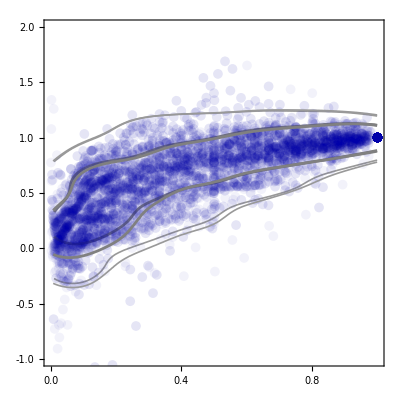

```mathematica
Clear[gdRListVel, gdRListVelFlat]
gdRListVel[gdFunction_] := gdRListVel[gdFunction] = gdFunction[{nRad, δVms, Vobs, δVobs}][[#]] & /@ Range[175];
gdRListVelFlat[gdFunction_] := Flatten[gdRListVel[gdFunction], 1];

list2RARRotVelAux = Select[gdRListVelFlat[gdR], #[[4]]/#[[3]] <  0.1 &] ; (*Includes only the velocity points with uncertainty lower than 10% of Vobs*)
list2RARRotVel = Drop[list2RARRotVelAuxᵀ, -2]ᵀ; (*Removes the columns on Vobs and δVobs*)

distRARRotVel = distributionSilverman[list2RARRotVel];

list1LimitsVel = FindHDPDFValues[distRARRotVel, oneAndTwoSigma];

plotBlueRARVel = plotBlueFunction[{list2RARRotVel, list1LimitsVel}] ; 
Show[plotBlueRARVel, plotBlueRAR]
```

Case without Bulge

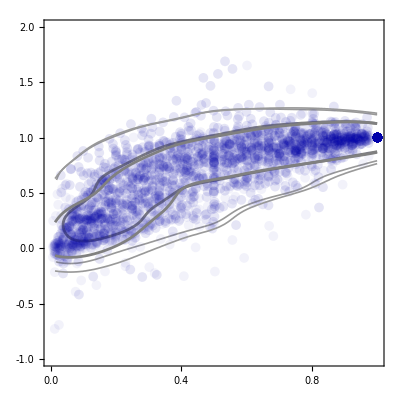

```mathematica
list2RARRotVelAuxNoBulge = Select[gdRListVelFlat[gdRBulgeless], #[[4]]/#[[3]] <  0.1 &] ; (*Includes only the velocity points with uncertainty lower than 10% of Vobs*)
list2RARRotVelNoBulge = Drop[list2RARRotVelAuxNoBulgeᵀ, -2]ᵀ; (*Removes the columns on Vobs and δVobs*)

distRARRotVelNoBulge = distributionSilverman[list2RARRotVelNoBulge];

list1LimitsVelNoBulge = FindHDPDFValues[distRARRotVelNoBulge, oneAndTwoSigma];

plotBlueRARVelNoBulge = plotBlueFunction[{list2RARRotVelNoBulge, list1LimitsVelNoBulge}] ; 
Show[plotBlueRARVelNoBulge, plotBlueRARNoBulge]
```

The plot below shows that the  excluded points most dense region is close to the galaxy center (as expectected, since there the observational velocity is typically close to zero, while the Vobs errors do not go to zero).

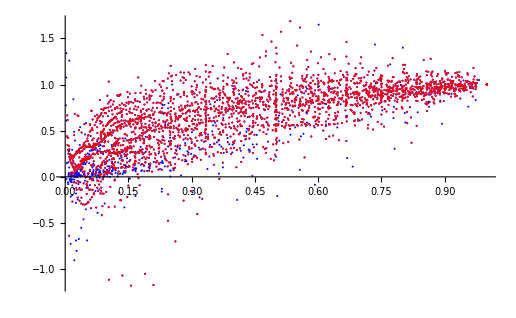

```mathematica
ListPlot[{ list2RARRot, list2RARRotVel}, PlotStyle-> {Blue, Red}]
```

The main differences appear in the lower bounds of the 1σ and 2σ regions, which get raised, in particular at r_n<0.2. The overall impact for our results is negligible. Since most of the excluded data points are close to the galactic center, in the bulgeless case the 1σ upper and lower limits get connected, which adds a nonnecessary computational complication and such case is artificial, since it depends on the choice of the 10% rejection limit).

```mathematica
Clear[list1InterpSigmaCurves, plotSigmaRegions];
list1InterpSigmaCurves::usage = "list1InterpSigmaCurves[blueplot] provides a list of 4 interpolated curves in the following order:"<> 
    "{1σLowerLimit, 1σUpperLimit, 2σLowerLimit, 2σUpperLimit}. /n"<>
    "The plot to be provided (blueplot) can be generated by the function plotBlue.";
list1InterpSigmaCurves[plotblue_] := Block[
  {
    sigmaContoursList,
    curveSigma, 
    curveOrder, 
    curve2SigmaNeg, 
    curve1SigmaNeg, 
    curve1SigmaPlus, 
    curve2SigmaPlus
  },
  sigmaContoursList = Cases[
    Normal @ FullForm @ First @ plotblue,
    Line[pts_] :> pts,
    Infinity
  ];
  curveSigma[n_] := Interpolation[
    Sort@sigmaContoursList⟦n⟧,
    Method -> "Spline", 
    InterpolationOrder-> 2
  ];
  curveOrder = Ordering @ Table[curveSigma[n][0.5], {n, 1, 4}];
  curve2SigmaNeg = curveSigma[curveOrder⟦1⟧];
  curve1SigmaNeg = curveSigma[curveOrder⟦2⟧];
  curve1SigmaPlus = curveSigma[curveOrder⟦3⟧];
  curve2SigmaPlus = curveSigma[curveOrder⟦4⟧];
  {
    curve1SigmaNeg,
    curve1SigmaPlus,
    curve2SigmaNeg, 
    curve2SigmaPlus
  }
];

plotSigmaRegions::usage = 
  "plotSigmaRegions[curvesSigma, xLimit1, xLimit2] yields a plot with the 1 and 2 sigma regions from xLimit1 to xLmit2. \n" <>
  "The standard values of xLimit1 and xLimit2 are 0.2 and 0.9. \n" <>
  "The input to be provided, curvesSigma, can be generated by list1InterpSigmaCurves.";
  
plotSigmaRegions[curvesSigma_, xLimit1_:0.01, xLimit2_:0.99] := Plot[
  {
    curvesSigma[[3]][r],
    curvesSigma[[1]][r],
    curvesSigma[[2]][r],
    curvesSigma[[4]][r]
  },
  {r, xLimit1, xLimit2},
  Filling -> {{1 -> {3}, GrayLevel[0.7]}, {2 -> {4}}},
  PlotStyle -> {{Thickness[0.002], Gray}, {Thickness @ 0.002, Gray}},
  FillingStyle -> {GrayLevel[0.7], Opacity @ 0.05}
];

(*EXECUTION*)

{plotSigmaRegionsRAR, plotSigmaRegionsRARNoBulge} = plotSigmaRegions[list1InterpSigmaCurves[#]] & /@ {plotBlueRAR, plotBlueRARNoBulge};

plotBackground[upperLimit_] := nPlot[
  100,
  {rn, 0, 1},
  PlotRange -> {{0, 1}, {-0.25, upperLimit}},
  AspectRatio -> (1 / 1.3),
  GridLines -> None, 
  Prolog -> {
    Dotted,
    Line @ {{0, 0}, {1, 0}},
    Gray,
    Opacity[0.2], 
    Rectangle[{0.001, -0.5},{0.2, upperLimit}],
    Rectangle[{0.9, -0.5},{0.999, upperLimit}]
  }
];

(*GraphicsRow[
  {plotSigmaRegionsRAR, plotSigmaRegionsRARNoBulge},
  ImageSize -> 800
]*)
```

### I.2.1. Exporting the σ regions into a almost-paper-ready table (uncomment to export the files)

```mathematica
Clear[exportSigmaList]
exportSigmaList::usage = "curvesSigmaList[listOfCurves, rnMin, rnMax, step] generates 1σ and 2σ limiting curves in a close-to-paper-ready formated table, /n"<>
  "with rMin < r < rMax, in steps provided by step (optional, 0.02 being standard). The listOfCurves can be generated by list1InterpSigmaCurves./n"<>
  "exportSigmaList does not exports any file, but prepares the list to be exported.";

exportSigmaList[list1IpSigmaCurves_, rnMin_, rnMax_, step_:0.025] := Block[
  {header, tab, rn, nF, tabAux},
  header = {"# rn", "1σLower", "1σUpper", "2σLower", "2σUpper"};
  nF := NumberForm[#, {4, 3}] &;
  tabAux = Table[list1IpSigmaCurves[[n]]@rn, {n, 4}];
  tab = Table[
    nF /@ Flatten[{rn, tabAux}],
    {rn, rnMin, rnMax, step} 
  ];
  Join[{header}, tab]
];

list1InterpCurvesRAR = list1InterpSigmaCurves[plotBlueRAR];
list1InterpCurvesRARNoBulge = list1InterpSigmaCurves[plotBlueRARNoBulge];

 
(*Export["sigmaRegionsRAR.csv", exportSigmaList[list1InterpCurvesRAR, 0.025, 1]];
Export["sigmaRegionsRARNoBulge.csv", exportSigmaList[list1InterpCurvesRARNoBulge, 0.025, 1]];*)
```

## I.3 NAV efficiency definition (inserted into the NAVbaseCode file), remove this after checking

```mathematica
(*δVobs1σL[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[1]][xn]; (*L stands for lower limit*)
δVobs1σU[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[2]][xn]; (*U stands for upper limit*)
δVobs2σL[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[3]][xn];
δVobs2σU[xn_] =  list1InterpSigmaCurves[plotBlueRAR][[4]][xn];

positivePart[x_] := HeavisideTheta[x] x;

Clear[areaObs];
areaObs[numberOfSigmas_] := Which[
  numberOfSigmas == 1, NIntegrate[δVobs1σU[xn] - δVobs1σL[xn], {xn, 0.2, 0.9}],
  numberOfSigmas == 2, NIntegrate[δVobs2σU[xn] - δVobs2σL[xn], {xn, 0.2, 0.9}],
  True, Echo["Wrong number of sigmas specification. Aborting."]; Abort[]
];
  
efficiencyNAV[ModelSigmaL_, ModelSigmaU_, numberOfSigmas_Integer] := Block[ (*There is another efficiencyNAV function with different number of arguments.*)
  {
    areaIntersection,
    areaModelOut,
    xn, (*equivalent to rn, used to avoid definition clash*)
    δVobsL,
    δVobsU
  },
  
  Which[
    numberOfSigmas == 1, δVobsL = δVobs1σL; δVobsU = δVobs1σU,
    numberOfSigmas == 2, δVobsL = δVobs2σL; δVobsU = δVobs2σU,
    True, Echo["Wrong number of sigmas specification. Aborting."]; Abort[]
  ];
  
  areaIntersection = NIntegrate[
    Min[δVobsU[xn], ModelSigmaU[xn]] - Max[δVobsL[xn], ModelSigmaL[xn]],
    {xn, 0.2, 0.9}
  ] / areaObs[numberOfSigmas];
  
  areaModelOut = NIntegrate[
    positivePart[ModelSigmaU[xn] - δVobsU[xn]] + positivePart[δVobsL[xn] - ModelSigmaL[xn]],
    {xn, 0.2, 0.9}
  ]/ areaObs[numberOfSigmas];
  
  {areaIntersection - areaModelOut, areaIntersection, areaModelOut}
];

Clear @ efficiencyNAVtotal; (*There is another efficiencyNAVtotal function with different number of arguments.*)
efficiencyNAVtotal[ModelSigmaL1_, ModelSigmaU1_, ModelSigmaL2_, ModelSigmaU2_] := (
  efficiencyNAV[ModelSigmaL1, ModelSigmaU1, 1] + 
  efficiencyNAV[ModelSigmaL2, ModelSigmaU2, 2]
) / 2;*)
```